## Use Stirling Numbers to Define Chromatic Polynomials

```mathematica
chromaticPolynomial[n_]:=Simplify[FunctionExpand[Sum[StirlingS2[n,i]*FactorialPower[q,i]*(q-i)^n,{i,1,n}]]]
```

```mathematica
chromaticRoots[n_]:=NSolve[chromaticPolynomial[n]==0, q,WorkingPrecision->2*Log[n]]
```

#### Magnitudes of Roots

```mathematica
chromaticRoots[28]
```

{{q→0},{q→1.},{q→2.},{q→3.},{q→4.},{q→5.},{q→6.},{q→7.},{q→8.},{q→9.},{q→10.},{q→11.},{q→12.},{q→12.9843},{q→13.5602-0.46181 ⅈ},{q→13.5602+0.46181 ⅈ},{q→13.9177-1.2911 ⅈ},{q→13.9177+1.2911 ⅈ},{q→14.2714-2.1665 ⅈ},{q→14.2714+2.1665 ⅈ},{q→14.6129-3.09128 ⅈ},{q→14.6129+3.09128 ⅈ},{q→14.9416-4.06834 ⅈ},{q→14.9416+4.06834 ⅈ},{q→15.2574-5.1009 ⅈ},{q→15.2574+5.1009 ⅈ},{q→15.5606-6.1929 ⅈ},{q→15.5606+6.1929 ⅈ},{q→15.8517-7.34915 ⅈ},{q→15.8517+7.34915 ⅈ},{q→16.1314-8.57539 ⅈ},{q→16.1314+8.57539 ⅈ},{q→16.4002-9.87841 ⅈ},{q→16.4002+9.87841 ⅈ},{q→16.6589-11.2663 ⅈ},{q→16.6589+11.2663 ⅈ},{q→16.9082-12.7485 ⅈ},{q→16.9082+12.7485 ⅈ},{q→17.149-14.3369 ⅈ},{q→17.149+14.3369 ⅈ},{q→17.3822-16.0458 ⅈ},{q→17.3822+16.0458 ⅈ},{q→17.6088-17.8939 ⅈ},{q→17.6088+17.8939 ⅈ},{q→17.8301-19.9059 ⅈ},{q→17.8301+19.9059 ⅈ},{q→18.0478-22.1163 ⅈ},{q→18.0478+22.1163 ⅈ},{q→18.2641-24.5766 ⅈ},{q→18.2641+24.5766 ⅈ},{q→18.4826-27.3712 ⅈ},{q→18.4826+27.3712 ⅈ},{q→18.7095-30.6614 ⅈ},{q→18.7095+30.6614 ⅈ},{q→18.9615-34.8611 ⅈ},{q→18.9615+34.8611 ⅈ}}

```mathematica
(*try for n=10*)
Abs[q/.chromaticRoots[10]]
```

{0.,1.,2.,3.,4.00037,4.86746,5.25673,5.25673,5.81053,5.81053,6.51764,6.51764,7.43619,7.43619,8.64425,8.64425,10.2702,10.2702,12.6146,12.6146}

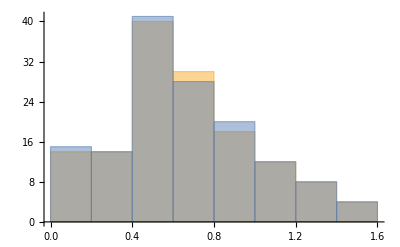

```mathematica
Histogram[Table[Abs[(q/n)/.chromaticRoots[n]],{n,70,71}]]
```

### Fitting Curves to Roots

```mathematica
filterRoots[roots_]:=Module[{newroots=List[]},
			For[i=1,i<=Length[roots], i++,If[Im[roots[[i]]]>0,AppendTo[newroots,roots[[i]]],0]];
Return[newroots]]
```

```mathematica
MapThread[List,{Re[Flatten[Table[filterRoots[(q/n - 4/(Pi*E))/.chromaticRoots[n]],{n,70,71}]]],Im[Flatten[Table[filterRoots[(q/n)/.chromaticRoots[n]],{n,70,71}]]]}]
```

{{0.00762594,0.00798533},{0.0128082,0.0193977},{0.0179333,0.0309921},{0.0229993,0.0428341},{0.0280047,0.0549304},{0.0329484,0.0672878},{0.0378294,0.0799135},{0.0426466,0.0928147},{0.0473991,0.105999},{0.0520864,0.119474},{0.0567078,0.133248},{0.0612631,0.147329},{0.0657521,0.161727},{0.070175,0.176451},{0.074532,0.19151},{0.0788235,0.206916},{0.0830502,0.22268},{0.0872125,0.238814},{0.0913114,0.255331},{0.0953477,0.272244},{0.0993224,0.289568},{0.103236,0.307318},{0.107091,0.325512},{0.110887,0.344165},{0.114626,0.363298},{0.118309,0.38293},{0.121938,0.403083},{0.125514,0.42378},{0.129039,0.445046},{0.132515,0.466908},{0.135943,0.489397},{0.139325,0.512544},{0.142664,0.536386},{0.145961,0.560961},{0.14922,0.586313},{0.152442,0.612491},{0.155631,0.63955},{0.15879,0.667552},{0.161922,0.696567},{0.165031,0.726678},{0.168121,0.75798},{0.171197,0.790585},{0.174265,0.824627},{0.177331,0.86027},{0.180404,0.897713},{0.183494,0.937213},{0.186614,0.979101},{0.189781,1.02382},{0.193021,1.07202},{0.196371,1.12463},{0.199894,1.18323},{0.203713,1.25084},{0.208155,1.3353},{0.00643493,0.00546171},{0.0114482,0.0164696},{0.0165168,0.0278368},{0.0215267,0.0394427},{0.0264781,0.0512938},{0.0313698,0.0633966},{0.036201,0.0757579},{0.0409704,0.0883846},{0.0456774,0.101284},{0.0503212,0.114463},{0.0549012,0.12793},{0.0594171,0.141692},{0.0638686,0.155758},{0.0682559,0.170137},{0.072579,0.184838},{0.0768384,0.199872},{0.0810345,0.215248},{0.0851679,0.230979},{0.0892392,0.247075},{0.0932493,0.26355},{0.097199,0.280417},{0.101089,0.297691},{0.104921,0.315386},{0.108696,0.33352},{0.112414,0.352108},{0.116077,0.37117},{0.119687,0.390726},{0.123244,0.410797},{0.126751,0.431406},{0.130209,0.452577},{0.133619,0.474338},{0.136983,0.496718},{0.140304,0.519749},{0.143583,0.543466},{0.146823,0.567907},{0.150026,0.593117},{0.153194,0.619143},{0.15633,0.64604},{0.159438,0.673868},{0.16252,0.702699},{0.165581,0.732613},{0.168624,0.763703},{0.171655,0.796082},{0.174679,0.829883},{0.177702,0.865265},{0.180733,0.902428},{0.183782,0.941626},{0.186861,0.983186},{0.189989,1.02755},{0.19319,1.07535},{0.1965,1.12751},{0.199983,1.18561},{0.203761,1.25264},{0.208156,1.33633}}

```mathematica
test=FindFit[MapThread[List,{Re[Flatten[Table[filterRoots[(q/n-4/(Pi*E))/.chromaticRoots[n]],{n,100,101}]]],Im[Flatten[Table[filterRoots[(q/n)/.chromaticRoots[n]],{n,100,101}]]]}],a*b^x+c,{a,b,c},x]
```

{a→0.112479,b→196901.,c→-0.0939158}

```mathematica
Log[(b/.test)]/Log[(/.)]
```

```mathematica
A/.test
```

4.42346

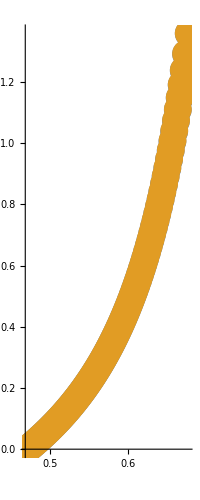

```mathematica
points=ComplexListPlot[Table[Flatten[filterRoots[(q/n)/.chromaticRoots[n]]],{n,100,101}], PlotStyle->PointSize[0.05]]
```

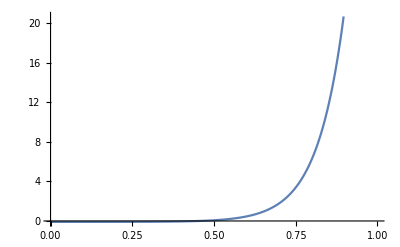

```mathematica
curve=Plot[(a/.test)*(b/.test)^(x-4/(Pi*E))+(c/.test),{x,0,1}]
```

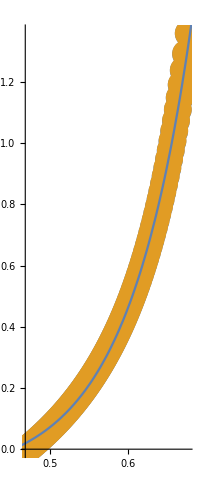

ComplexListPlot::lpn: {{},{{0.75,0.433013}},«8»,«10»} is not a list of numbers or pairs of numbers.

ComplexListPlot[{{},{0.75+0.433013 ⅈ},{0.619787+0.164045 ⅈ,0.713547+0.649561 ⅈ},{0.535774+0.0393191 ⅈ,0.638603+0.340307 ⅈ,0.700622+0.774361 ⅈ},{0.590063+0.196832 ⅈ,0.646877+0.466417 ⅈ,0.693873+0.858237 ⅈ},{0.555994+0.114805 ⅈ,0.60859+0.30877 ⅈ,0.651674+0.560847 ⅈ,0.689742+0.919445 ⅈ},{0.530795+0.0647865 ⅈ,0.579303+0.212891 ⅈ,0.619898+0.39761 ⅈ,0.654825+0.634878 ⅈ,0.686972+0.966538 ⅈ},{0.504844+0.0292997 ⅈ,0.55598+0.148768 ⅈ,0.594505+0.293596 ⅈ,0.627613+0.470455 ⅈ,0.657068+0.694849 ⅈ,0.685001+1.00415 ⅈ},{0.536932+0.103212 ⅈ,0.573567+0.221582 ⅈ,0.605224+0.361873 ⅈ,0.633231+0.531581 ⅈ,0.658759+0.744643 ⅈ,0.683537+1.03503 ⅈ},{0.521111+0.069105 ⅈ,0.555961+0.168909 ⅈ,0.586307+0.284676 ⅈ,0.613212+0.420642 ⅈ,0.637514+0.583787 ⅈ,0.660089+0.786794 ⅈ,0.682414+1.06094 ⅈ},{0.508788+0.0433958 ⅈ,0.540958+0.128842 ⅈ,0.570055+0.227018 ⅈ,0.595989+0.340046 ⅈ,0.619405+0.471909 ⅈ,0.640896+0.629012 ⅈ,0.661169+0.823037 ⅈ,0.68153+1.08306 ⅈ},{0.495593+0.0242671 ⅈ,0.52806+0.0974375 ⅈ,0.555928+0.182383 ⅈ,0.580951+0.278813 ⅈ,0.603609+0.389146 ⅈ,0.624352+0.517122 ⅈ,0.64364+0.668652 ⅈ,0.662069+0.854605 ⅈ,0.680821+1.10222 ⅈ},{0.516905+0.0722859 ⅈ,0.543543+0.146876 ⅈ,0.567685+0.230741 ⅈ,0.589642+0.325351 ⅈ,0.609768+0.433064 ⅈ,0.628401+0.55736 ⅈ,0.645916+0.703743 ⅈ,0.662835+0.8824 ⅈ,0.680243+1.11899 ⅈ},{0.507051+0.0516228 ⅈ,0.532614+0.118013 ⅈ,0.555893+0.192037 ⅈ,0.577178+0.274668 ⅈ,0.596744+0.367456 ⅈ,0.614855+0.472634 ⅈ,0.63178+0.593452 ⅈ,0.647838+0.735071 ⅈ,0.663496+0.9071 ⅈ,0.679764+1.13384 ⅈ},{0.49899+0.0343111 ⅈ,0.52292+0.0941348 ⅈ,0.545347+0.160244 ⅈ,0.565979+0.23345 ⅈ,0.585012+0.314792 ⅈ,0.60266+0.405778 ⅈ,0.619129+0.508513 ⅈ,0.634645+0.626046 ⅈ,0.649486+0.763247 ⅈ,0.664076+0.929227 ⅈ,0.679363+1.14709 ⅈ},{0.490975+0.0211104 ⅈ,0.514286+0.0740748 ⅈ,0.53587+0.133696 ⅈ,0.55586+0.199295 ⅈ,0.574378+0.271585 ⅈ,0.591592+0.351619 ⅈ,0.607667+0.440838 ⅈ,0.622775+0.541225 ⅈ,0.637109+0.655657 ⅈ,0.650917+0.788753 ⅈ,0.66459+0.949187 ⅈ,0.679024+1.159 ⅈ},{0.506592+0.0570257 ⅈ,0.527321+0.111221 ⅈ,0.546678+0.170553 ⅈ,0.564692+0.235511 ⅈ,0.581487+0.306841 ⅈ,0.597198+0.385569 ⅈ,0.611963+0.473063 ⅈ,0.625924+0.571197 ⅈ,0.639252+0.682701 ⅈ,0.652173+0.811974 ⅈ,0.665051+0.967302 ⅈ,0.678735+1.16978 ⅈ},{0.499588+0.0423687 ⅈ,0.519584+0.0919691 ⅈ,0.538314+0.146053 ⅈ,0.555832+0.204951 ⅈ,0.572218+0.269202 ⅈ,0.587583+0.339552 ⅈ,0.602035+0.416987 ⅈ,0.61569+0.502803 ⅈ,0.628673+0.59878 ⅈ,0.641136+0.707518 ⅈ,0.653287+0.833223 ⅈ,0.665466+0.983833 ⅈ,0.678487+1.17959 ⅈ},{0.493501+0.0293649 ⅈ,0.512561+0.0753084 ⅈ,0.530673+0.124938 ⅈ,0.5477+0.178747 ⅈ,0.563686+0.23713 ⅈ,0.578712+0.30064 ⅈ,0.59287+0.370004 ⅈ,0.606252+0.446163 ⅈ,0.618956+0.530352 ⅈ,0.631095+0.624265 ⅈ,0.642806+0.730389 ⅈ,0.654281+0.852756 ⅈ,0.665844+0.998992 ⅈ,0.678272+1.18857 ⅈ},{0.488041+0.0189819 ⅈ,0.506164+0.0607534 ⅈ,0.523673+0.106565 ⅈ,0.540216+0.156042 ⅈ,0.555807+0.209484 ⅈ,0.570502+0.267306 ⅈ,0.584374+0.330055 ⅈ,0.597501+0.398436 ⅈ,0.609962+0.473345 ⅈ,0.621844+0.555959 ⅈ,0.633247+0.647898 ⅈ,0.644298+0.751548 ⅈ,0.655177+0.870786 ⅈ,0.66619+1.01295 ⅈ,0.678085+1.19682 ⅈ}}]

```mathematica
Show[points,curve]
```

```mathematica
chromaticRoots[10]
```

### Real Plot of Polynomials

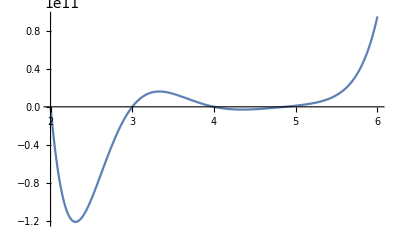

```mathematica
Plot[chromaticPolynomial[10],{q,2,6}]
```

```mathematica
Plot[chromaticPolynomial[20],{q,-0.1,11}]
```

-Graphics-

### Complex Plot of Polynomials

```mathematica
ComplexPlot3D[chromaticPolynomial[5],{q,-2-2I,2+2I},ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
fit=FindFit[MapThread[List,{Table[n,{n,2,20}],Table[chromaticPolynomial[n]/.q->5,{n,2,20}]}], a*b^x,{a,b,c},x]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→226.166,b→5.31235,c→1.}

```mathematica
pointsEval=ListPlot[MapThread[List,{Table[n,{n,2,20}],Table[chromaticPolynomial[n]/.q->5,{n,2,20}]}]]
```

-Graphics-

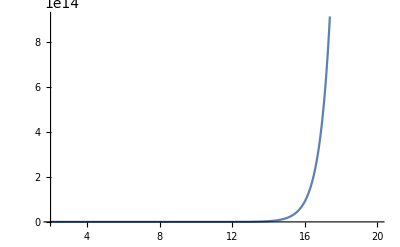

```mathematica
curveEval=Plot[(a/.fit)*(b/.fit)^x+(c/.fit),{x,2,20}]
```

```mathematica
Show[{pointsEval,curveEval}]
```

-Graphics-

```mathematica
ListPlot[Table[StirlingS2[40,i],{i,0,40}]]
```

-Graphics-

```mathematica
N[StirlingS2[40,14]/StirlingS2[40,15]]
```

1.25404

```mathematica
Flatten[Table[Position[Table[StirlingS2[n,i],{i,0,n}],Max[Table[StirlingS2[n,i],{i,0,n}]]],{n,0,60}]]
```

{1,2,2,3,3,3,4,4,5,5,5,6,6,6,7,7,7,8,8,8,9,9,9,10,10,10,11,11,11,11,12,12,12,13,13,13,13,14,14,14,15,15,15,15,16,16,16,16,17,17,17,17,18,18,18,18,19,19,19,19,20,20}

```mathematica
N[StirlingS2[60,19]/StirlingS2[60,20]]
```

1.1379

```mathematica
rootsChromaticExample=Flatten[Table[(q/n)/.chromaticRoots[n],{n,2,35}]]
```

{0,0.5,0.7-0.4 ⅈ,0.7+0.4 ⅈ,0,0.33,0.62-0.2 ⅈ,0.62+0.2 ⅈ,0.71-0.65 ⅈ,0.71+0.65 ⅈ,0,0.25,0.54-0.04 ⅈ,0.54+0.04 ⅈ,0.64-0.34 ⅈ,0.64+0.34 ⅈ,0.7-0.77 ⅈ,0.7+0.77 ⅈ,0,0.2,0.401,0.537,0.59-0.2 ⅈ,0.59+0.2 ⅈ,0.647-0.466 ⅈ,0.647+0.466 ⅈ,0.694-0.858 ⅈ,0.694+0.858 ⅈ,0,0.167,0.333,0.488,0.556-0.115 ⅈ,0.556+0.115 ⅈ,0.609-0.309 ⅈ,0.609+0.309 ⅈ,0.652-0.561 ⅈ,0.652+0.561 ⅈ,0.69-0.919 ⅈ,0.69+0.919 ⅈ,0,0.143,0.286,0.428,0.5308-0.0648 ⅈ,0.5308+0.0648 ⅈ,0.5793-0.213 ⅈ,0.5793+0.213 ⅈ,0.62-0.398 ⅈ,0.62+0.398 ⅈ,0.655-0.635 ⅈ,0.655+0.635 ⅈ,0.687-0.967 ⅈ,0.687+0.967 ⅈ,0,0.125,0.25,0.375,0.5048-0.0293 ⅈ,0.5048+0.0293 ⅈ,0.556-0.149 ⅈ,0.556+0.149 ⅈ,0.5945-0.294 ⅈ,0.5945+0.294 ⅈ,0.6276-0.4705 ⅈ,0.6276+0.4705 ⅈ,0.6571-0.6948 ⅈ,0.6571+0.6948 ⅈ,0.685-1.004 ⅈ,0.685+1.004 ⅈ,0,0.1111,0.2222,0.3333,0.4457,0.5052,0.5369-0.103 ⅈ,0.5369+0.103 ⅈ,0.5736-0.2216 ⅈ,0.5736+0.2216 ⅈ,0.6052-0.3619 ⅈ,0.6052+0.3619 ⅈ,0.6332-0.5316 ⅈ,0.6332+0.5316 ⅈ,0.6588-0.7446 ⅈ,0.6588+0.7446 ⅈ,0.6835-1.035 ⅈ,0.6835+1.035 ⅈ,0,0.1,0.2,0.3,0.4,0.4867,0.5211-0.0691 ⅈ,0.5211+0.0691 ⅈ,0.556-0.1689 ⅈ,0.556+0.1689 ⅈ,0.5863-0.2847 ⅈ,0.5863+0.2847 ⅈ,0.6132-0.4206 ⅈ,0.6132+0.4206 ⅈ,0.6375-0.5838 ⅈ,0.6375+0.5838 ⅈ,0.6601-0.7868 ⅈ,0.6601+0.7868 ⅈ,0.6824-1.061 ⅈ,0.6824+1.061 ⅈ,0,0.09091,0.1818,0.2727,0.3636,0.4533,0.5088-0.0434 ⅈ,0.5088+0.0434 ⅈ,0.541-0.1288 ⅈ,0.541+0.1288 ⅈ,0.5701-0.227 ⅈ,0.5701+0.227 ⅈ,0.596-0.34 ⅈ,0.596+0.34 ⅈ,0.6194-0.4719 ⅈ,0.6194+0.4719 ⅈ,0.6409-0.629 ⅈ,0.6409+0.629 ⅈ,0.6612-0.823 ⅈ,0.6612+0.823 ⅈ,0.6815-1.083 ⅈ,0.6815+1.083 ⅈ,0,0.08333,0.1667,0.25,0.3333,0.4166,0.49559-0.0243 ⅈ,0.49559+0.0243 ⅈ,0.52806-0.09744 ⅈ,0.52806+0.09744 ⅈ,0.55593-0.1824 ⅈ,0.55593+0.1824 ⅈ,0.58095-0.2788 ⅈ,0.58095+0.2788 ⅈ,0.60361-0.3891 ⅈ,0.60361+0.3891 ⅈ,0.62435-0.5171 ⅈ,0.62435+0.5171 ⅈ,0.6436-0.6687 ⅈ,0.6436+0.6687 ⅈ,0.6621-0.8546 ⅈ,0.6621+0.8546 ⅈ,0.6808-1.1022 ⅈ,0.6808+1.1022 ⅈ,0,0.076923,0.15385,0.23077,0.30769,0.38461,0.46363,0.49265,0.51691-0.07229 ⅈ,0.51691+0.07229 ⅈ,0.54354-0.1469 ⅈ,0.54354+0.1469 ⅈ,0.56769-0.2307 ⅈ,0.56769+0.2307 ⅈ,0.58964-0.3254 ⅈ,0.58964+0.3254 ⅈ,0.60977-0.43306 ⅈ,0.60977+0.43306 ⅈ,0.6284-0.55736 ⅈ,0.6284+0.55736 ⅈ,0.64592-0.70374 ⅈ,0.64592+0.70374 ⅈ,0.66283-0.8824 ⅈ,0.66283+0.8824 ⅈ,0.6802-1.119 ⅈ,0.6802+1.119 ⅈ,0,0.071429,0.14286,0.21429,0.28571,0.35714,0.42864,0.48551,0.50705-0.05162 ⅈ,0.50705+0.05162 ⅈ,0.53261-0.118 ⅈ,0.53261+0.118 ⅈ,0.55589-0.192 ⅈ,0.55589+0.192 ⅈ,0.57718-0.27467 ⅈ,0.57718+0.27467 ⅈ,0.59674-0.36746 ⅈ,0.59674+0.36746 ⅈ,0.61485-0.47263 ⅈ,0.61485+0.47263 ⅈ,0.63178-0.59345 ⅈ,0.63178+0.59345 ⅈ,0.64784-0.73507 ⅈ,0.64784+0.73507 ⅈ,0.6635-0.9071 ⅈ,0.6635+0.9071 ⅈ,0.67976-1.1338 ⅈ,0.67976+1.1338 ⅈ,0,0.066667,0.13333,0.2,0.26667,0.33333,0.4,0.46478,0.49899-0.03431 ⅈ,0.49899+0.03431 ⅈ,0.52292-0.09413 ⅈ,0.52292+0.09413 ⅈ,0.54535-0.16024 ⅈ,0.54535+0.16024 ⅈ,0.56598-0.23345 ⅈ,0.56598+0.23345 ⅈ,0.58501-0.31479 ⅈ,0.58501+0.31479 ⅈ,0.60266-0.40578 ⅈ,0.60266+0.40578 ⅈ,0.61913-0.50851 ⅈ,0.61913+0.50851 ⅈ,0.63465-0.62605 ⅈ,0.63465+0.62605 ⅈ,0.64949-0.76325 ⅈ,0.64949+0.76325 ⅈ,0.66408-0.92923 ⅈ,0.66408+0.92923 ⅈ,0.67936-1.1471 ⅈ,0.67936+1.1471 ⅈ,0,0.0625,0.125,0.1875,0.25,0.3125,0.375,0.43741,0.49097-0.02111 ⅈ,0.49097+0.02111 ⅈ,0.51429-0.07407 ⅈ,0.51429+0.07407 ⅈ,0.53587-0.1337 ⅈ,0.53587+0.1337 ⅈ,0.55586-0.19929 ⅈ,0.55586+0.19929 ⅈ,0.57438-0.27159 ⅈ,0.57438+0.27159 ⅈ,0.59159-0.35162 ⅈ,0.59159+0.35162 ⅈ,0.60767-0.44084 ⅈ,0.60767+0.44084 ⅈ,0.62278-0.54122 ⅈ,0.62278+0.54122 ⅈ,0.63711-0.65566 ⅈ,0.63711+0.65566 ⅈ,0.65092-0.78875 ⅈ,0.65092+0.78875 ⅈ,0.66459-0.94919 ⅈ,0.66459+0.94919 ⅈ,0.67902-1.159 ⅈ,0.67902+1.159 ⅈ,0,0.058824,0.11765,0.17647,0.23529,0.29412,0.35294,0.41176,0.47643,0.48238,0.50659-0.05703 ⅈ,0.50659+0.05703 ⅈ,0.52732-0.11122 ⅈ,0.52732+0.11122 ⅈ,0.54668-0.17055 ⅈ,0.54668+0.17055 ⅈ,0.56469-0.23551 ⅈ,0.56469+0.23551 ⅈ,0.58149-0.30684 ⅈ,0.58149+0.30684 ⅈ,0.5972-0.38557 ⅈ,0.5972+0.38557 ⅈ,0.61196-0.47306 ⅈ,0.61196+0.47306 ⅈ,0.62592-0.5712 ⅈ,0.62592+0.5712 ⅈ,0.63925-0.6827 ⅈ,0.63925+0.6827 ⅈ,0.65217-0.81197 ⅈ,0.65217+0.81197 ⅈ,0.66505-0.9673 ⅈ,0.66505+0.9673 ⅈ,0.67874-1.1698 ⅈ,0.67874+1.1698 ⅈ,0,0.055556,0.11111,0.16667,0.22222,0.27778,0.33333,0.38889,0.44457,0.48409,0.49959-0.04237 ⅈ,0.49959+0.04237 ⅈ,0.51958-0.091969 ⅈ,0.51958+0.091969 ⅈ,0.53831-0.14605 ⅈ,0.53831+0.14605 ⅈ,0.55583-0.20495 ⅈ,0.55583+0.20495 ⅈ,0.57222-0.2692 ⅈ,0.57222+0.2692 ⅈ,0.58758-0.33955 ⅈ,0.58758+0.33955 ⅈ,0.60204-0.41699 ⅈ,0.60204+0.41699 ⅈ,0.61569-0.5028 ⅈ,0.61569+0.5028 ⅈ,0.62867-0.59878 ⅈ,0.62867+0.59878 ⅈ,0.64114-0.70752 ⅈ,0.64114+0.70752 ⅈ,0.65329-0.83322 ⅈ,0.65329+0.83322 ⅈ,0.66547-0.98383 ⅈ,0.66547+0.98383 ⅈ,0.67849-1.1796 ⅈ,0.67849+1.1796 ⅈ,0,0.052632,0.10526,0.15789,0.21053,0.26316,0.31579,0.36842,0.42106,0.47084,0.493501-0.02936 ⅈ,0.493501+0.02936 ⅈ,0.512561-0.075308 ⅈ,0.512561+0.075308 ⅈ,0.530673-0.12494 ⅈ,0.530673+0.12494 ⅈ,0.5477-0.17875 ⅈ,0.5477+0.17875 ⅈ,0.563686-0.23713 ⅈ,0.563686+0.23713 ⅈ,0.57871-0.30064 ⅈ,0.57871+0.30064 ⅈ,0.59287-0.37 ⅈ,0.59287+0.37 ⅈ,0.60625-0.44616 ⅈ,0.60625+0.44616 ⅈ,0.61896-0.53035 ⅈ,0.61896+0.53035 ⅈ,0.63109-0.62427 ⅈ,0.63109+0.62427 ⅈ,0.64281-0.73039 ⅈ,0.64281+0.73039 ⅈ,0.65428-0.85276 ⅈ,0.65428+0.85276 ⅈ,0.66584-0.99899 ⅈ,0.66584+0.99899 ⅈ,0.67827-1.1886 ⅈ,0.67827+1.1886 ⅈ,0,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.44984,0.488041-0.01898 ⅈ,0.488041+0.01898 ⅈ,0.506164-0.060753 ⅈ,0.506164+0.060753 ⅈ,0.523673-0.10656 ⅈ,0.523673+0.10656 ⅈ,0.540216-0.15604 ⅈ,0.540216+0.15604 ⅈ,0.555807-0.20948 ⅈ,0.555807+0.20948 ⅈ,0.570502-0.26731 ⅈ,0.570502+0.26731 ⅈ,0.584374-0.33006 ⅈ,0.584374+0.33006 ⅈ,0.597501-0.39844 ⅈ,0.597501+0.39844 ⅈ,0.609962-0.47334 ⅈ,0.609962+0.47334 ⅈ,0.621844-0.55596 ⅈ,0.621844+0.55596 ⅈ,0.63325-0.6479 ⅈ,0.63325+0.6479 ⅈ,0.6443-0.751548 ⅈ,0.6443+0.751548 ⅈ,0.65518-0.870786 ⅈ,0.65518+0.870786 ⅈ,0.66619-1.01295 ⅈ,0.66619+1.01295 ⅈ,0.67808-1.19682 ⅈ,0.67808+1.19682 ⅈ,0,0.047619,0.0952381,0.142857,0.190476,0.238095,0.285714,0.333333,0.380952,0.428565,0.479963-0.008019 ⅈ,0.479963+0.008019 ⅈ,0.500344-0.047935 ⅈ,0.500344+0.047935 ⅈ,0.517245-0.090443 ⅈ,0.517245+0.090443 ⅈ,0.533311-0.13619 ⅈ,0.533311+0.13619 ⅈ,0.548511-0.18542 ⅈ,0.548511+0.18542 ⅈ,0.562879-0.23844 ⅈ,0.562879+0.23844 ⅈ,0.576473-0.29567 ⅈ,0.576473+0.29567 ⅈ,0.589355-0.35765 ⅈ,0.589355+0.35765 ⅈ,0.601592-0.425055 ⅈ,0.601592+0.425055 ⅈ,0.613253-0.49874 ⅈ,0.613253+0.49874 ⅈ,0.624416-0.579832 ⅈ,0.624416+0.579832 ⅈ,0.635173-0.669885 ⅈ,0.635173+0.669885 ⅈ,0.645641-0.771193 ⅈ,0.645641+0.771193 ⅈ,0.655988-0.88749 ⅈ,0.655988+0.88749 ⅈ,0.66651-1.02586 ⅈ,0.66651+1.02586 ⅈ,0.67792-1.20444 ⅈ,0.67792+1.20444 ⅈ,0,0.0454545,0.0909091,0.136364,0.181818,0.227273,0.272727,0.318182,0.363636,0.409091,0.454785,0.482566,0.494972-0.036607 ⅈ,0.494972+0.036607 ⅈ,0.51133-0.07619 ⅈ,0.51133+0.07619 ⅈ,0.526925-0.1187 ⅈ,0.526925+0.1187 ⅈ,0.54174-0.16429 ⅈ,0.54174+0.16429 ⅈ,0.555785-0.2132 ⅈ,0.555785+0.2132 ⅈ,0.569105-0.26576 ⅈ,0.569105+0.26576 ⅈ,0.581749-0.322388 ⅈ,0.581749+0.322388 ⅈ,0.593772-0.383599 ⅈ,0.593772+0.383599 ⅈ,0.605234-0.450039 ⅈ,0.605234+0.450039 ⅈ,0.616194-0.522531 ⅈ,0.616194+0.522531 ⅈ,0.626724-0.602154 ⅈ,0.626724+0.602154 ⅈ,0.636908-0.690403 ⅈ,0.636908+0.690403 ⅈ,0.646856-0.78949 ⅈ,0.646856+0.78949 ⅈ,0.656727-0.90302 ⅈ,0.656727+0.90302 ⅈ,0.666801-1.03784 ⅈ,0.666801+1.03784 ⅈ,0.677777-1.2115 ⅈ,0.677777+1.2115 ⅈ,0,0.0434783,0.0869565,0.130435,0.173913,0.217391,0.26087,0.304348,0.347826,0.391304,0.434791,0.474171,0.490049-0.02628 ⅈ,0.490049+0.02628 ⅈ,0.505875-0.063503 ⅈ,0.505875+0.063503 ⅈ,0.521009-0.10317 ⅈ,0.521009+0.10317 ⅈ,0.535442-0.14559 ⅈ,0.535442+0.14559 ⅈ,0.549169-0.19095 ⅈ,0.549169+0.19095 ⅈ,0.562217-0.239513 ⅈ,0.562217+0.239513 ⅈ,0.574627-0.291596 ⅈ,0.574627+0.291596 ⅈ,0.586444-0.347609 ⅈ,0.586444+0.347609 ⅈ,0.597717-0.408051 ⅈ,0.597717+0.408051 ⅈ,0.608496-0.473543 ⅈ,0.608496+0.473543 ⅈ,0.618837-0.544873 ⅈ,0.618837+0.544873 ⅈ,0.628806-0.623079 ⅈ,0.628806+0.623079 ⅈ,0.63848-0.709603 ⅈ,0.63848+0.709603 ⅈ,0.647962-0.806582 ⅈ,0.647962+0.806582 ⅈ,0.657404-0.917502 ⅈ,0.657404+0.917502 ⅈ,0.667074-1.049 ⅈ,0.667074+1.049 ⅈ,0.67765-1.21805 ⅈ,0.67765+1.21805 ⅈ,0,0.0416667,0.0833333,0.125,0.166667,0.208333,0.25,0.291667,0.333333,0.375,0.416667,0.458029,0.485924-0.017508 ⅈ,0.485924+0.017508 ⅈ,0.500829-0.05214 ⅈ,0.500829+0.05214 ⅈ,0.515516-0.089309 ⅈ,0.515516+0.089309 ⅈ,0.529574-0.12894 ⅈ,0.529574+0.12894 ⅈ,0.542987-0.17121 ⅈ,0.542987+0.17121 ⅈ,0.555767-0.216298 ⅈ,0.555767+0.216298 ⅈ,0.567945-0.264477 ⅈ,0.567945+0.264477 ⅈ,0.57956-0.316068 ⅈ,0.57956+0.316068 ⅈ,0.590652-0.371462 ⅈ,0.590652+0.371462 ⅈ,0.601262-0.431142 ⅈ,0.601262+0.431142 ⅈ,0.611437-0.495702 ⅈ,0.611437+0.495702 ⅈ,0.621228-0.565902 ⅈ,0.621228+0.565902 ⅈ,0.630695-0.642742 ⅈ,0.630695+0.642742 ⅈ,0.639911-0.727617 ⅈ,0.639911+0.727617 ⅈ,0.648973-0.822591 ⅈ,0.648973+0.822591 ⅈ,0.658026-0.931046 ⅈ,0.658026+0.931046 ⅈ,0.667329-1.05941 ⅈ,0.667329+1.05941 ⅈ,0.677537-1.22417 ⅈ,0.677537+1.22417 ⅈ,0,0.04,0.08,0.12,0.16,0.2,0.24,0.28,0.32,0.36,0.4,0.439988,0.480125-0.00961 ⅈ,0.480125+0.00961 ⅈ,0.496164-0.041898 ⅈ,0.496164+0.041898 ⅈ,0.510409-0.076855 ⅈ,0.510409+0.076855 ⅈ,0.524098-0.11403 ⅈ,0.524098+0.11403 ⅈ,0.537199-0.153563 ⅈ,0.537199+0.153563 ⅈ,0.549714-0.195623 ⅈ,0.549714+0.195623 ⅈ,0.561664-0.240415 ⅈ,0.561664+0.240415 ⅈ,0.57308-0.288198 ⅈ,0.57308+0.288198 ⅈ,0.583994-0.339287 ⅈ,0.583994+0.339287 ⅈ,0.594443-0.394062 ⅈ,0.594443+0.394062 ⅈ,0.604466-0.452987 ⅈ,0.604466+0.452987 ⅈ,0.614103-0.516635 ⅈ,0.614103+0.516635 ⅈ,0.623402-0.585737 ⅈ,0.623402+0.585737 ⅈ,0.632418-0.661262 ⅈ,0.632418+0.661262 ⅈ,0.641221-0.744556 ⅈ,0.641221+0.744556 ⅈ,0.649903-0.837625 ⅈ,0.649903+0.837625 ⅈ,0.658601-0.943745 ⅈ,0.658601+0.943745 ⅈ,0.667566-1.06916 ⅈ,0.667566+1.06916 ⅈ,0.677437-1.22989 ⅈ,0.677437+1.22989 ⅈ,0,0.0384615,0.0769231,0.115385,0.153846,0.192308,0.230769,0.269231,0.307692,0.346154,0.384615,0.423076,0.462023,0.480901,0.491827-0.032665 ⅈ,0.491827+0.032665 ⅈ,0.505651-0.06561 ⅈ,0.505651+0.06561 ⅈ,0.518979-0.10059 ⅈ,0.518979+0.10059 ⅈ,0.531773-0.137711 ⅈ,0.531773+0.137711 ⅈ,0.544026-0.177098 ⅈ,0.544026+0.177098 ⅈ,0.55575-0.218923 ⅈ,0.55575+0.218923 ⅈ,0.566968-0.263395 ⅈ,0.566968+0.263395 ⅈ,0.577708-0.31077 ⅈ,0.577708+0.31077 ⅈ,0.588001-0.361352 ⅈ,0.588001+0.361352 ⅈ,0.597879-0.41551 ⅈ,0.597879+0.41551 ⅈ,0.607376-0.473691 ⅈ,0.607376+0.473691 ⅈ,0.61653-0.536446 ⅈ,0.61653+0.536446 ⅈ,0.625387-0.604483 ⅈ,0.625387+0.604483 ⅈ,0.633997-0.67874 ⅈ,0.633997+0.67874 ⅈ,0.642425-0.760522 ⅈ,0.642425+0.760522 ⅈ,0.65076-0.851774 ⅈ,0.65076+0.851774 ⅈ,0.659134-0.955682 ⅈ,0.659134+0.955682 ⅈ,0.667789-1.07832 ⅈ,0.667789+1.07832 ⅈ,0.677347-1.23525 ⅈ,0.677347+1.23525 ⅈ,0,0.037037,0.0740741,0.111111,0.148148,0.185185,0.222222,0.259259,0.296296,0.333333,0.37037,0.407407,0.444462,0.475949,0.487716-0.024157 ⅈ,0.487716+0.024157 ⅈ,0.501211-0.055407 ⅈ,0.501211+0.055407 ⅈ,0.514186-0.088432 ⅈ,0.514186+0.088432 ⅈ,0.526679-0.123394 ⅈ,0.526679+0.123394 ⅈ,0.538673-0.160408 ⅈ,0.538673+0.160408 ⅈ,0.550173-0.199614 ⅈ,0.550173+0.199614 ⅈ,0.561196-0.241182 ⅈ,0.561196+0.241182 ⅈ,0.571764-0.28532 ⅈ,0.571764+0.28532 ⅈ,0.581903-0.332278 ⅈ,0.581903+0.332278 ⅈ,0.591641-0.382352 ⅈ,0.591641+0.382352 ⅈ,0.601006-0.435897 ⅈ,0.601006+0.435897 ⅈ,0.610031-0.493345 ⅈ,0.610031+0.493345 ⅈ,0.618751-0.555228 ⅈ,0.618751+0.555228 ⅈ,0.627207-0.622233 ⅈ,0.627207+0.622233 ⅈ,0.635448-0.695268 ⅈ,0.635448+0.695268 ⅈ,0.643536-0.7756 ⅈ,0.643536+0.7756 ⅈ,0.651554-0.865121 ⅈ,0.651554+0.865121 ⅈ,0.659629-0.966928 ⅈ,0.659629+0.966928 ⅈ,0.667999-1.08693 ⅈ,0.667999+1.08693 ⅈ,0.677268-1.24029 ⅈ,0.677268+1.24029 ⅈ,0,0.0357143,0.0714286,0.107143,0.142857,0.178571,0.214286,0.25,0.285714,0.321429,0.357143,0.392857,0.428572,0.463726,0.484294-0.016493 ⅈ,0.484294+0.016493 ⅈ,0.497059-0.04611 ⅈ,0.497059+0.04611 ⅈ,0.509694-0.077373 ⅈ,0.509694+0.077373 ⅈ,0.521889-0.110403 ⅈ,0.521889+0.110403 ⅈ,0.533628-0.145298 ⅈ,0.533628+0.145298 ⅈ,0.544907-0.182175 ⅈ,0.544907+0.182175 ⅈ,0.555736-0.221175 ⅈ,0.555736+0.221175 ⅈ,0.566134-0.26247 ⅈ,0.566134+0.26247 ⅈ,0.576121-0.306264 ⅈ,0.576121+0.306264 ⅈ,0.585722-0.3528 ⅈ,0.585722+0.3528 ⅈ,0.594961-0.402366 ⅈ,0.594961+0.402366 ⅈ,0.603866-0.455304 ⅈ,0.603866+0.455304 ⅈ,0.612465-0.512031 ⅈ,0.612465+0.512031 ⅈ,0.620791-0.573065 ⅈ,0.620791+0.573065 ⅈ,0.628884-0.639069 ⅈ,0.628884+0.639069 ⅈ,0.636789-0.710925 ⅈ,0.636789+0.710925 ⅈ,0.644564-0.789867 ⅈ,0.644564+0.789867 ⅈ,0.652291-0.877735 ⅈ,0.652291+0.877735 ⅈ,0.660092-0.977545 ⅈ,0.660092+0.977545 ⅈ,0.668197-1.09505 ⅈ,0.668197+1.09505 ⅈ,0.677196-1.24504 ⅈ,0.677196+1.24504 ⅈ,0,0.0344828,0.0689655,0.103448,0.137931,0.172414,0.206897,0.241379,0.275862,0.310345,0.344828,0.37931,0.413793,0.448251,0.480047-0.010125 ⅈ,0.480047+0.010125 ⅈ,0.493173-0.037595 ⅈ,0.493173+0.037595 ⅈ,0.505475-0.067276 ⅈ,0.505475+0.067276 ⅈ,0.517381-0.0985644 ⅈ,0.517381+0.0985644 ⅈ,0.528868-0.131556 ⅈ,0.528868+0.131556 ⅈ,0.539927-0.16635 ⅈ,0.539927+0.16635 ⅈ,0.550565-0.203065 ⅈ,0.550565+0.203065 ⅈ,0.560794-0.241842 ⅈ,0.560794+0.241842 ⅈ,0.570631-0.282852 ⅈ,0.570631+0.282852 ⅈ,0.580098-0.326295 ⅈ,0.580098+0.326295 ⅈ,0.589214-0.372407 ⅈ,0.589214+0.372407 ⅈ,0.598004-0.421466 ⅈ,0.598004+0.421466 ⅈ,0.606491-0.473804 ⅈ,0.606491+0.473804 ⅈ,0.614704-0.529824 ⅈ,0.614704+0.529824 ⅈ,0.622672-0.590029 ⅈ,0.622672+0.590029 ⅈ,0.630433-0.655063 ⅈ,0.630433+0.655063 ⅈ,0.638031-0.725784 ⅈ,0.638031+0.725784 ⅈ,0.64552-0.803392 ⅈ,0.64552+0.803392 ⅈ,0.652978-0.889679 ⅈ,0.652978+0.889679 ⅈ,0.660525-0.987587 ⅈ,0.660525+0.987587 ⅈ,0.668384-1.10273 ⅈ,0.668384+1.10273 ⅈ,0.677132-1.24952 ⅈ,0.677132+1.24952 ⅈ,0,0.0333333,0.0666667,0.1,0.133333,0.166667,0.2,0.233333,0.266667,0.3,0.333333,0.366667,0.4,0.433332,0.467749,0.478884,0.48954-0.029798 ⅈ,0.48954+0.029798 ⅈ,0.501509-0.0580206 ⅈ,0.501509+0.0580206 ⅈ,0.513132-0.0877338 ⅈ,0.513132+0.0877338 ⅈ,0.524371-0.119007 ⅈ,0.524371+0.119007 ⅈ,0.535214-0.151928 ⅈ,0.535214+0.151928 ⅈ,0.545662-0.186595 ⅈ,0.545662+0.186595 ⅈ,0.555723-0.223129 ⅈ,0.555723+0.223129 ⅈ,0.565412-0.26167 ⅈ,0.565412+0.26167 ⅈ,0.574746-0.302386 ⅈ,0.574746+0.302386 ⅈ,0.583742-0.345473 ⅈ,0.583742+0.345473 ⅈ,0.59242-0.39116 ⅈ,0.59242+0.39116 ⅈ,0.600802-0.439716 ⅈ,0.600802+0.439716 ⅈ,0.60891-0.491462 ⅈ,0.60891+0.491462 ⅈ,0.616771-0.54679 ⅈ,0.616771+0.54679 ⅈ,0.624413-0.606188 ⅈ,0.624413+0.606188 ⅈ,0.63187-0.670281 ⅈ,0.63187+0.670281 ⅈ,0.639185-0.739907 ⅈ,0.639185+0.739907 ⅈ,0.64641-0.816234 ⅈ,0.64641+0.816234 ⅈ,0.65362-0.901009 ⅈ,0.65362+0.901009 ⅈ,0.660932-0.997103 ⅈ,0.660932+0.997103 ⅈ,0.668562-1.10999 ⅈ,0.668562+1.10999 ⅈ,0.677074-1.25376 ⅈ,0.677074+1.25376 ⅈ,0,0.0322581,0.0645161,0.0967742,0.129032,0.16129,0.193548,0.225806,0.258065,0.290323,0.322581,0.354839,0.387097,0.419355,0.451649,0.476788,0.4860445-0.022584 ⅈ,0.4860445+0.022584 ⅈ,0.4977759-0.0495066 ⅈ,0.4977759+0.0495066 ⅈ,0.5091222-0.0777892 ⅈ,0.5091222+0.0777892 ⅈ,0.5201175-0.107506 ⅈ,0.5201175+0.107506 ⅈ,0.5307472-0.138733 ⅈ,0.5307472+0.138733 ⅈ,0.541007-0.171557 ⅈ,0.541007+0.171557 ⅈ,0.550903-0.206078 ⅈ,0.550903+0.206078 ⅈ,0.560445-0.242416 ⅈ,0.560445+0.242416 ⅈ,0.569646-0.280711 ⅈ,0.569646+0.280711 ⅈ,0.578523-0.321127 ⅈ,0.578523+0.321127 ⅈ,0.587093-0.363855 ⅈ,0.587093+0.363855 ⅈ,0.595374-0.409117 ⅈ,0.595374+0.409117 ⅈ,0.603384-0.457174 ⅈ,0.603384+0.457174 ⅈ,0.611147-0.508337 ⅈ,0.611147+0.508337 ⅈ,0.618686-0.562988 ⅈ,0.618686+0.562988 ⅈ,0.626028-0.621599 ⅈ,0.626028+0.621599 ⅈ,0.633206-0.684782 ⅈ,0.633206+0.684782 ⅈ,0.64026-0.753351 ⅈ,0.64026+0.753351 ⅈ,0.647242-0.828446 ⅈ,0.647242+0.828446 ⅈ,0.654222-0.911774 ⅈ,0.654222+0.911774 ⅈ,0.661314-1.00614 ⅈ,0.661314+1.00614 ⅈ,0.66873-1.11688 ⅈ,0.66873+1.11688 ⅈ,0.677021-1.25778 ⅈ,0.677021+1.25778 ⅈ,0,0.03125,0.0625,0.09375,0.125,0.15625,0.1875,0.21875,0.25,0.28125,0.3125,0.34375,0.375,0.40625,0.437501,0.467758,0.4830139-0.015809 ⅈ,0.4830139+0.015809 ⅈ,0.4942551-0.0416503 ⅈ,0.4942551+0.0416503 ⅈ,0.5053341-0.068627 ⅈ,0.5053341+0.068627 ⅈ,0.5160911-0.0969265 ⅈ,0.5160911+0.0969265 ⅈ,0.5265105-0.126617 ⅈ,0.5265105+0.126617 ⅈ,0.536585-0.157772 ⅈ,0.536585+0.157772 ⅈ,0.5463163-0.190479 ⅈ,0.5463163+0.190479 ⅈ,0.5557117-0.224839 ⅈ,0.5557117+0.224839 ⅈ,0.5647824-0.260971 ⅈ,0.5647824+0.260971 ⅈ,0.5735419-0.299013 ⅈ,0.5735419+0.299013 ⅈ,0.5820046-0.339125 ⅈ,0.5820046+0.339125 ⅈ,0.5901863-0.381493 ⅈ,0.5901863+0.381493 ⅈ,0.598104-0.426331 ⅈ,0.598104+0.426331 ⅈ,0.605775-0.473894 ⅈ,0.605775+0.473894 ⅈ,0.613222-0.524484 ⅈ,0.613222+0.524484 ⅈ,0.620465-0.578472 ⅈ,0.620465+0.578472 ⅈ,0.627532-0.636318 ⅈ,0.627532+0.636318 ⅈ,0.634453-0.698619 ⅈ,0.634453+0.698619 ⅈ,0.641266-0.766167 ⅈ,0.641266+0.766167 ⅈ,0.648021-0.840078 ⅈ,0.648021+0.840078 ⅈ,0.654787-0.922018 ⅈ,0.654787+0.922018 ⅈ,0.661674-1.014724 ⅈ,0.661674+1.014724 ⅈ,0.66889-1.123428 ⅈ,0.66889+1.123428 ⅈ,0.676974-1.261594 ⅈ,0.676974+1.261594 ⅈ,0,0.030303,0.0606061,0.0909091,0.121212,0.151515,0.181818,0.212121,0.242424,0.272727,0.30303,0.333333,0.363636,0.393939,0.424242,0.454495,0.4798165-0.010266 ⅈ,0.4798165+0.010266 ⅈ,0.4909288-0.034372 ⅈ,0.4909288+0.034372 ⅈ,0.501751-0.0601593 ⅈ,0.501751+0.0601593 ⅈ,0.5122753-0.0871646 ⅈ,0.5122753+0.0871646 ⅈ,0.5224877-0.115454 ⅈ,0.5224877+0.115454 ⅈ,0.532379-0.145093 ⅈ,0.532379+0.145093 ⅈ,0.5419475-0.176157 ⅈ,0.5419475+0.176157 ⅈ,0.5511979-0.208732 ⅈ,0.5511979+0.208732 ⅈ,0.5601388-0.242919 ⅈ,0.5601388+0.242919 ⅈ,0.5687815-0.278837 ⅈ,0.5687815+0.278837 ⅈ,0.5771383-0.31662 ⅈ,0.5771383+0.31662 ⅈ,0.585223-0.356425 ⅈ,0.585223+0.356425 ⅈ,0.5930501-0.398431 ⅈ,0.5930501+0.398431 ⅈ,0.6006354-0.442849 ⅈ,0.6006354+0.442849 ⅈ,0.607996-0.489924 ⅈ,0.607996+0.489924 ⅈ,0.6151513-0.539951 ⅈ,0.6151513+0.539951 ⅈ,0.6221227-0.593291 ⅈ,0.6221227+0.593291 ⅈ,0.628935-0.6503927 ⅈ,0.628935+0.6503927 ⅈ,0.635618-0.7118376 ⅈ,0.635618+0.7118376 ⅈ,0.642208-0.7784013 ⅈ,0.642208+0.7784013 ⅈ,0.648752-0.8511724 ⅈ,0.648752+0.8511724 ⅈ,0.655319-0.93178 ⅈ,0.655319+0.93178 ⅈ,0.662015-1.022902 ⅈ,0.662015+1.022902 ⅈ,0.669043-1.129656 ⅈ,0.669043+1.129656 ⅈ,0.676932-1.265219 ⅈ,0.676932+1.265219 ⅈ,0,0.02941176,0.05882353,0.08823529,0.1176471,0.1470588,0.1764706,0.2058824,0.2352941,0.2647059,0.2941176,0.3235294,0.3529412,0.3823529,0.4117647,0.4411745,0.4745663-0.001645 ⅈ,0.4745663+0.001645 ⅈ,0.4877998-0.027623 ⅈ,0.4877998+0.027623 ⅈ,0.4983578-0.0523104 ⅈ,0.4983578+0.0523104 ⅈ,0.5086553-0.0781298 ⅈ,0.5086553+0.0781298 ⅈ,0.5186646-0.105138 ⅈ,0.5186646+0.105138 ⅈ,0.5283751-0.133393 ⅈ,0.5283751+0.133393 ⅈ,0.5377826-0.162962 ⅈ,0.5377826+0.162962 ⅈ,0.5468893-0.193919 ⅈ,0.5468893+0.193919 ⅈ,0.5557014-0.22635 ⅈ,0.5557014+0.22635 ⅈ,0.564228-0.260356 ⅈ,0.564228+0.260356 ⅈ,0.5724799-0.296052 ⅈ,0.5724799+0.296052 ⅈ,0.5804688-0.333573 ⅈ,0.5804688+0.333573 ⅈ,0.5882074-0.373068 ⅈ,0.5882074+0.373068 ⅈ,0.5957094-0.414714 ⅈ,0.5957094+0.414714 ⅈ,0.6029895-0.458714 ⅈ,0.6029895+0.458714 ⅈ,0.610064-0.5053078 ⅈ,0.610064+0.5053078 ⅈ,0.6169512-0.5547824 ⅈ,0.6169512+0.5547824 ⅈ,0.6236714-0.6074889 ⅈ,0.6236714+0.6074889 ⅈ,0.6302485-0.6638666 ⅈ,0.6302485+0.6638666 ⅈ,0.6367106-0.7244823 ⅈ,0.6367106+0.7244823 ⅈ,0.6430927-0.7900945 ⅈ,0.6430927+0.7900945 ⅈ,0.649441-0.8617677 ⅈ,0.649441+0.8617677 ⅈ,0.655821-0.9410959 ⅈ,0.655821+0.9410959 ⅈ,0.662338-1.0307 ⅈ,0.662338+1.0307 ⅈ,0.669189-1.13559 ⅈ,0.669189+1.13559 ⅈ,0.676893-1.268671 ⅈ,0.676893+1.268671 ⅈ,0,0.02857143,0.05714286,0.08571429,0.1142857,0.1428571,0.1714286,0.2,0.2285714,0.2571429,0.2857143,0.3142857,0.3428571,0.3714286,0.4,0.4285714,0.4572165,0.4770346,0.4847829-0.021357 ⅈ,0.4847829+0.021357 ⅈ,0.4951409-0.0450148 ⅈ,0.4951409+0.0450148 ⅈ,0.5052177-0.0697445 ⅈ,0.5052177+0.0697445 ⅈ,0.5150281-0.0955766 ⅈ,0.5150281+0.0955766 ⅈ,0.5245604-0.122565 ⅈ,0.5245604+0.122565 ⅈ,0.5338088-0.150768 ⅈ,0.5338088+0.150768 ⅈ,0.5427731-0.180251 ⅈ,0.5427731+0.180251 ⅈ,0.5514574-0.211088 ⅈ,0.5514574+0.211088 ⅈ,0.5598688-0.243365 ⅈ,0.5598688+0.243365 ⅈ,0.5680164-0.277183 ⅈ,0.5680164+0.277183 ⅈ,0.5759104-0.312654 ⅈ,0.5759104+0.312654 ⅈ,0.5835618-0.349908 ⅈ,0.5835618+0.349908 ⅈ,0.5909826-0.3890936 ⅈ,0.5909826+0.3890936 ⅈ,0.5981854-0.4303804 ⅈ,0.5981854+0.4303804 ⅈ,0.6051844-0.4739668 ⅈ,0.6051844+0.4739668 ⅈ,0.6119949-0.5200863 ⅈ,0.6119949+0.5200863 ⅈ,0.6186342-0.5690189 ⅈ,0.6186342+0.5690189 ⅈ,0.6251219-0.621107 ⅈ,0.6251219+0.621107 ⅈ,0.6314805-0.67678 ⅈ,0.6314805+0.67678 ⅈ,0.6377371-0.7365917 ⅈ,0.6377371+0.7365917 ⅈ,0.6439256-0.8012842 ⅈ,0.6439256+0.8012842 ⅈ,0.6500905-0.8718992 ⅈ,0.6500905+0.8718992 ⅈ,0.6562957-0.9499973 ⅈ,0.6562957+0.9499973 ⅈ,0.662643-1.038145 ⅈ,0.662643+1.038145 ⅈ,0.669328-1.141252 ⅈ,0.669328+1.141252 ⅈ,0.676858-1.271963 ⅈ,0.676858+1.271963 ⅈ}

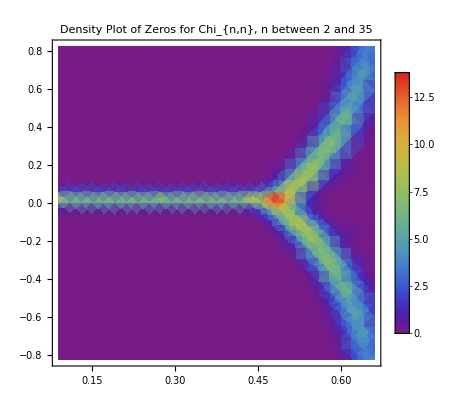

```mathematica
SmoothDensityHistogram[MapThread[List,{Re[rootsChromaticExample],Im[rootsChromaticExample]}],0.02,"PDF",ColorFunction->"Rainbow",Mesh->0,PlotLegends->Automatic,PlotLabel->"Density Plot of Zeros for Chi_{n,n}, n between 2 and 35"]
```